```mathematica
(*sx={{0,1},{1,0}}/2*)
```

```mathematica
(*sy={{0,-I},{I,0}}/2*)
```

```mathematica
(*sz={{1,0},{0,-1}}/2*)
```

```mathematica
(*e= {{1,0},{0,1}}*)
```

```mathematica
(*{{1,0},{0,1}}*)
```

```mathematica
(*z={{0,0},{0,0}}*)
```

```mathematica
(*Sza = TensorProduct[sz,e]//ArrayFlatten*)
```

```mathematica
(*Szb= TensorProduct[e, sz]//ArrayFlatten*)
```

```mathematica
(*Sxa=TensorProduct[sx,e]//ArrayFlatten*)
```

```mathematica
(*Sxb= TensorProduct[e, sx]//ArrayFlatten*)
```

```mathematica
(*Sya=TensorProduct[sy,e]//ArrayFlatten*)
```

```mathematica
(*Syb= TensorProduct[e, sy]//ArrayFlatten*)
```

```mathematica
(*EE= TensorProduct[e, e]/2//ArrayFlatten*)
```

```mathematica
(*ZZ= TensorProduct[z, z]//ArrayFlatten*)
```

```mathematica
(*SxSx=2TensorProduct[sx,sx]//ArrayFlatten*)
```

```mathematica
(*SxSy=2TensorProduct[sx,sy]//ArrayFlatten*)
```

```mathematica
(*SxSz=2TensorProduct[sx,sz]//ArrayFlatten*)
```

```mathematica
(*SySx=2TensorProduct[sy,sx]//ArrayFlatten*)
```

```mathematica
(*SySy=2TensorProduct[sy,sy]//ArrayFlatten*)
```

```mathematica
(*SySz=2TensorProduct[sy,sz]//ArrayFlatten*)
```

```mathematica
(*SzSx=2TensorProduct[sz,sx]//ArrayFlatten*)
```

```mathematica
(*SzSy=2TensorProduct[sz,sy]//ArrayFlatten*)
```

```mathematica
(*SzSz=2TensorProduct[sz,sz]//ArrayFlatten*)
```

```mathematica
(* S1= {Sxa, Sya,Sza} *)
```

```mathematica
(* S2= {Sxb, Syb,Szb} *)
```

```mathematica
(*ProductBasis = {EE, Sxa,Sya,Sza,Sxb,Syb,Szb,SxSx,SxSy,SxSz,SySx,SySy,SySz,SzSx,SzSy,SzSz}*)
```

```mathematica
(* ProductBasisAlpha = {"EE", "S1x","S1y","S1z","S2x","S2y","S2z","S1xS2x","S1xS2y","S1xS2z","S1yS2x","S1yS2y","S1yS2z","S1zS2x","S1zS2y","S1zS2z"} *)
```

```mathematica
(*ProductBasisAlpha = {"EE", "Sxa","Sya","Sza","Sxb","Syb","Szb","SxSx","SxSy","SxSz","SySx","SySy","SySz","SzSx","SzSy","SzSz"}*)
```

```mathematica
(*ProductBasisIndex=Table[i, {i,Length[ProductBasis]}]*)
```

```mathematica
(*MatrixTrace[a_]:= Module[{sum=0,i}, For[i=1,i<=Length[a[[1]]], i++, sum=sum+a[[i,i]]]; sum]*)
```

```mathematica
(*BasisProject[a_]:=Module[{i,out=Table[0, {i,Length[ProductBasis]}]}, For[i=1,i<= Length[ProductBasis],i++, out[[i]]=MatrixTrace[ProductBasis[[i]].a]]; out]*)
```

```mathematica
(*BasisProjectAlpha[a_] :=Simplify[ BasisProject[a].ProductBasisAlpha] *)
```

```mathematica
(*comm[a_,b_]:= a.b-b.a*)
```

```mathematica
(*cComm[a_,b_]:= comm[a,comm[a,b]]*)
```

```mathematica
(*PropagateBaseOp[a_,b_, ξ_]:= Module[{index=BasisProject[b].ProductBasisIndex, out= ZZ},If[Simplify[comm[a,b]]==ZZ,out=a,out=MatrixExp[-I*ξ*b].a.MatrixExp[I*ξ*b]; out= ExpToTrig[out]];TrigReduce[out]]*)
```

```mathematica
(*PropagateOp[a_,b_, ξ_]:= Module[{prop=ZZ, coff=0},For[i=1,i<=16,i++, coff=BasisProject[a][[i]];If[ToString[coff]!="0",  prop= prop+coff*PropagateBaseOp[ProductBasis[[i]],b,ξ]]]; prop]*)
```

```mathematica
rhoS=EE/2-(SxSx+SySy+SzSz)/2  (* Q_S = 1/4 - S_a.S_b *)
```

{{0,0,0,0},{0,1/2,-1/2,0},{0,-1/2,1/2,0},{0,0,0,0}}

```mathematica
rhoT=(3EE/2+(SxSx+SySy+SzSz)/2)/3 (* Q_T = 3/4 + S_a.S_b *)
```

{{1/3,0,0,0},{0,1/6,1/6,0},{0,1/6,1/6,0},{0,0,0,1/3}}

```mathematica
rhoT0=3EE/2+(SxSx+SySy+SzSz)/2 -(Sza+Szb).(Sza+Szb)(* Q_T0 = 3Q_T-(Sza+Szb)^2 *)
```

{{0,0,0,0},{0,1/2,1/2,0},{0,1/2,1/2,0},{0,0,0,0}}

```mathematica
rhoS+rhoT0
```

{{0,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}}

```mathematica
rhoud = {{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}
```

{{0,0,0,0},{0,1,0,0},{0,0,0,0},{0,0,0,0}}

```mathematica
rhodu = {{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}}
```

{{0,0,0,0},{0,0,0,0},{0,0,1,0},{0,0,0,0}}

```mathematica
rho0= {{0,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,0}} /2
```

{{0,0,0,0},{0,1/2,0,0},{0,0,-1/2,0},{0,0,0,0}}

```mathematica
(* H0a= Sza*Omegaa+ Szb*Omegab+ dmJ*SzSz- dp2J*(SxSx+SySy) *)
```

```mathematica
(* Eigensystem[H0a] *)
```

```mathematica
(* Reorder= {{0,1,0,0}, {0,0,0,1},{0,0,1,0},{1,0,0,0}} *)
```

```mathematica
(* H0aEVa//FullSimplify *)
```

```mathematica
(* H0aEVaR=Reorder.H0aEVa//FullSimplify *)
```

```mathematica
(* H0aEVeR=Reorder.H0aEVe *)
```

```mathematica
(*H0=q(Sza-Szb)+ dmJ*SzSz (* ω_s(Sza+Szb) omitted *)*)
```

```mathematica
rho0e=PropagateOp[rho0,(SxSy-SySx), ξ/2]
```

{{0,0,0,0},{0,Cos[ξ]/2,-Sin[ξ]/2,0},{0,-Sin[ξ]/2,-Cos[ξ]/2,0},{0,0,0,0}}

```mathematica
rho0eA=BasisProjectAlpha[rho0e]//FullSimplify
```

1/2 ((Sza-Szb) Cos[ξ]-(SxSx+SySy) Sin[ξ])

```mathematica
rho1e=PropagateOp[rho0e,Sza,q*T]//Simplify
```

{{0,0,0,0},{0,Cos[ξ]/2,-1/2 (Cos[q T]-ⅈ Sin[q T]) Sin[ξ],0},{0,-1/2 (Cos[q T]+ⅈ Sin[q T]) Sin[ξ],-Cos[ξ]/2,0},{0,0,0,0}}

```mathematica
rho1e=PropagateOp[rho1e,Szb,-q*T]//Simplify
```

{{0,0,0,0},{0,Cos[ξ]/2,-1/2 (Cos[2 q T]-ⅈ Sin[2 q T]) Sin[ξ],0},{0,-1/2 (Cos[2 q T]+ⅈ Sin[2 q T]) Sin[ξ],-Cos[ξ]/2,0},{0,0,0,0}}

```mathematica
rho1e=PropagateOp[rho1e,SzSz,dmJ*T]//FullSimplify
```

{{0,0,0,0},{0,Cos[ξ]/2,-1/2 ⅇ^(-2 ⅈ q T) Sin[ξ],0},{0,-1/2 ⅇ^(2 ⅈ q T) Sin[ξ],-Cos[ξ]/2,0},{0,0,0,0}}

```mathematica
(* rho1woZQCe = T/(2π)Integrate[ rho1e, {q,0,2π/T}]- MatrixTrace[rho1e]/MatrixTrace[EE]EE//FullSimplify *) (* ZQCs and trace omitted *)
```

```mathematica
rho1woZQCe = T/(2π)Integrate[ rho1e, {q,0,2π/T}]//FullSimplify (* ZQCs omitted *)
```

{{0,0,0,0},{0,Cos[ξ]/2,0,0},{0,0,-Cos[ξ]/2,0},{0,0,0,0}}

```mathematica
rho1woZQC=PropagateOp[rho1woZQCe, (SxSy-SySx), -ξ/2]//FullSimplify
```

{{0,0,0,0},{0,Cos[ξ]^2/2,1/2 Cos[ξ] Sin[ξ],0},{0,1/2 Cos[ξ] Sin[ξ],-1/2 Cos[ξ]^2,0},{0,0,0,0}}

```mathematica
rho2=PropagateOp[rho1woZQC, (Sxa+Sxb), β]//FullSimplify
```

{{1/4 Cos[ξ] Sin[β]^2 Sin[ξ],-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]+Cos[β] Sin[ξ]),1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]-Cos[β] Sin[ξ]),1/4 Cos[ξ] Sin[β]^2 Sin[ξ]},{1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]+Cos[β] Sin[ξ]),1/4 Cos[ξ] (2 Cos[β] Cos[ξ]-Sin[β]^2 Sin[ξ]),1/16 (3+Cos[2 β]) Sin[2 ξ],1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]+Cos[β] Sin[ξ])},{-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]-Cos[β] Sin[ξ]),1/16 (3+Cos[2 β]) Sin[2 ξ],-1/4 Cos[ξ] (2 Cos[β] Cos[ξ]+Sin[β]^2 Sin[ξ]),-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]-Cos[β] Sin[ξ])},{1/4 Cos[ξ] Sin[β]^2 Sin[ξ],-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]+Cos[β] Sin[ξ]),1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ]-Cos[β] Sin[ξ]),1/4 Cos[ξ] Sin[β]^2 Sin[ξ]}}

```mathematica
rho2e=PropagateOp[rho2, (SxSy-SySx), ξ/2]//FullSimplify
```

{{1/4 Cos[ξ] Sin[β]^2 Sin[ξ],-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (1+(-1+Cos[β]) Sin[ξ]),-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (-1+(-1+Cos[β]) Sin[ξ]),1/4 Cos[ξ] Sin[β]^2 Sin[ξ]},{1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (1+(-1+Cos[β]) Sin[ξ]),1/16 (8 Cos[β] Cos[ξ]^3+Sin[ξ] (-4 Cos[ξ] Sin[β]^2+(3+Cos[2 β]) Sin[2 ξ])),Cos[ξ]^2 Sin[β/2]^4 Sin[ξ],1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (1+(-1+Cos[β]) Sin[ξ])},{1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (-1+(-1+Cos[β]) Sin[ξ]),Cos[ξ]^2 Sin[β/2]^4 Sin[ξ],1/16 (-8 Cos[β] Cos[ξ]^3-Sin[ξ] (4 Cos[ξ] Sin[β]^2+(3+Cos[2 β]) Sin[2 ξ])),1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (-1+(-1+Cos[β]) Sin[ξ])},{1/4 Cos[ξ] Sin[β]^2 Sin[ξ],-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]+Sin[ξ/2]) (1+(-1+Cos[β]) Sin[ξ]),-1/4 ⅈ Cos[ξ] Sin[β] (Cos[ξ/2]-Sin[ξ/2]) (-1+(-1+Cos[β]) Sin[ξ]),1/4 Cos[ξ] Sin[β]^2 Sin[ξ]}}

```mathematica
coeffs= BasisProject[rho2e]//FullSimplify
```

{0,0,1/2 Cos[ξ/2] (Cos[β] (-1+Cos[ξ])-Cos[ξ]) Cos[ξ] Sin[β],1/16 (8 Cos[β] Cos[ξ]^3+(3+Cos[2 β]) Sin[ξ] Sin[2 ξ]),0,1/2 Cos[ξ] Sin[β] (Cos[ξ/2]+(-1+Cos[β]) Sin[ξ/2] Sin[ξ]),-1/8 Cos[ξ] (4 Cos[β] Cos[ξ]^2+(3+Cos[2 β]) Sin[ξ]^2),1/4 Cos[ξ] (4 Cos[ξ] Sin[β/2]^4+Sin[β]^2) Sin[ξ],0,0,0,1/4 Cos[ξ] (4 Cos[ξ] Sin[β/2]^4-Sin[β]^2) Sin[ξ],-1/4 (Cos[β]+(-1+Cos[β]) Cos[ξ]) Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2]),0,-1/4 (Cos[β]+(-1+Cos[β]) Cos[ξ]) Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2]),1/4 Sin[β]^2 Sin[2 ξ]}

```mathematica
coeffs.ProductBasisAlpha
```

1/2 Sya Cos[ξ/2] (Cos[β] (-1+Cos[ξ])-Cos[ξ]) Cos[ξ] Sin[β]+1/4 SySy Cos[ξ] (4 Cos[ξ] Sin[β/2]^4-Sin[β]^2) Sin[ξ]+1/4 SxSx Cos[ξ] (4 Cos[ξ] Sin[β/2]^4+Sin[β]^2) Sin[ξ]+1/2 Syb Cos[ξ] Sin[β] (Cos[ξ/2]+(-1+Cos[β]) Sin[ξ/2] Sin[ξ])-1/8 Szb Cos[ξ] (4 Cos[β] Cos[ξ]^2+(3+Cos[2 β]) Sin[ξ]^2)-1/4 SySz (Cos[β]+(-1+Cos[β]) Cos[ξ]) Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])-1/4 SzSy (Cos[β]+(-1+Cos[β]) Cos[ξ]) Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])+1/4 SzSz Sin[β]^2 Sin[2 ξ]+1/16 Sza (8 Cos[β] Cos[ξ]^3+(3+Cos[2 β]) Sin[ξ] Sin[2 ξ])

```mathematica
Y1=coeffs[[3]]//TrigExpand//FullSimplify
```

1/4 (Cos[β] (-1+Cos[ξ])-Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[β]

```mathematica
Y2=coeffs[[6]]// TrigExpand//FullSimplify
```

-1/4 (Cos[β] (-1+Cos[ξ])-Cos[ξ]) (Cos[ξ/2]+Cos[(3 ξ)/2]) Sin[β]

```mathematica
Y2==-Y1//FullSimplify
```

True

```mathematica
YZ= coeffs[[13]]
```

-1/4 (Cos[β]+(-1+Cos[β]) Cos[ξ]) Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
YZ= coeffs[[15]]
```

-1/4 (Cos[β]+(-1+Cos[β]) Cos[ξ]) Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
ZY== ZY //FullSimplify
```

True

```mathematica
(* Sya-Syb Path *)
```

```mathematica
(*rho3e=PropagateOp[(Sya-Syb), SzSz, dmJ]//FullSimplify*)
```

```mathematica
(*rho3e=PropagateOp[rho3e, (Sza-Szb), q]//FullSimplify*)
```

```mathematica
(*rho3= PropagateOp[rho3e,(SxSy-SySx),-ξ/2]//ExpToTrig//FullSimplify*)
```

```mathematica
(*rho4=PropagateOp[rho3 ,(Sxa+Sxb), π]//FullSimplify*)
```

```mathematica
(*rho4e= PropagateOp[rho4,(SxSy-SySx),ξ/2]//ExpToTrig//FullSimplify*)
```

```mathematica
(*rho5e= PropagateOp[rho4e, SzSz,dmJ]//FullSimplify*)
```

```mathematica
(*rho5e= PropagateOp[rho5e,(Sza-Szb),q]//FullSimplify*)
```

```mathematica
(*rho5= PropagateOp[rho5e,(SxSy-SySx),-ξ/2]//ExpToTrig// FullSimplify*)
```

```mathematica
(*rho5Integ=Integrate[rho5, {q,0,2π}]/(2π)//FullSimplify*)
```

```mathematica
(*coeffs=BasisProject[rho5Integ]//ExpToTrig //FullSimplify*)
```

```mathematica
(*coeffs[[2]]==coeffs[[5]]*)
```

```mathematica
(*coeffs[[3]]==-coeffs[[6]]*)
```

```mathematica
(*XpXYmYcoeff= coeffs[[2]]//ExpToTrig //FullSimplify*)
```

```mathematica
(* XpXYmYcoeff= -2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ] *)
```

```mathematica
(*coeffs[[13]]==coeffs[[15]]*)
```

```mathematica
(*coeffs[[10]]==-coeffs[[14]]*)
```

```mathematica
XpXYmYcoeff=1/2 Sin[2 dmJ] (Sin[ξ/2]-Sin[(3 ξ)/2])
```

1/2 Sin[2 dmJ] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
(*YZpZYYmYcoeff= coeffs[[13]]//ExpToTrig //FullSimplify*)
```

```mathematica
(*YZpZYYmYcoeff=1/2 Cos[2 dmJ] (-Sin[ξ/2]+Sin[(3 ξ)/2])*)
```

```mathematica
(* SySz+ SzSy path *)
```

```mathematica
(*ρ=PropagateOp[SySz+SzSy, SzSz,dmJ]*)
```

```mathematica
(*ρ = PropagateOp[ρ, (Sza-Szb),q]//FullSimplify*)
```

```mathematica
(*ρ = PropagateOp[ρ, (SxSy-SySx), -ξ/2]//FullSimplify*)
```

```mathematica
(*ρ = PropagateOp[ρ, (Sxa+Sxb), π]//FullSimplify*)
```

```mathematica
(*ρ = PropagateOp[ρ, (SxSy-SySx), ξ/2]//FullSimplify*)
```

```mathematica
(*ρ=PropagateOp[ρ, SzSz,dmJ]//FullSimplify*)
```

```mathematica
(*ρ=PropagateOp[ρ, (Sza-Szb),q]//FullSimplify*)
```

```mathematica
(*ρ=PropagateOp[ρ,(SxSy-SySx), -ξ/2]//FullSimplify*)
```

```mathematica
(*ρInt=Integrate[ρ, {q,0,2π}]/(2π)//ExpToTrig// Simplify*)
```

```mathematica
(*coeffs= BasisProject[ρInt]//FullSimplify*)
```

```mathematica
(*coeffs[[2]]==coeffs[[5]]*)
```

```mathematica
(*coeffs[[3]]==-coeffs[[6]]*)
```

```mathematica
(*XpXYZpZYcoeff=coeffs[[2]]*)
```

```mathematica
(*XpXYZpZYcoeff=-2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ]*)
```

```mathematica
XpXYZpZYcoeff=-2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ]
```

-2 Cos[dmJ] Cos[ξ/2] Cos[ξ] Sin[dmJ]

```mathematica
XpXYmYpathcoeff= XpXYmYcoeff*Y1//FullSimplify
```

1/4 Cos[ξ]^2 (Cos[β]+Cos[ξ]-Cos[β] Cos[ξ]) Sin[2 dmJ] Sin[β] Sin[ξ]

```mathematica
XpXYZpZYpathcoeff=XpXYZpZYcoeff*YZ //FullSimplify
```

1/2 Cos[dmJ] Cos[ξ/2] Cos[ξ] (Cos[β]+(-1+Cos[β]) Cos[ξ]) Sin[dmJ] Sin[β] (Sin[ξ/2]-Sin[(3 ξ)/2])

```mathematica
XpXcombinedcoeff=XpXYmYpathcoeff+XpXYZpZYpathcoeff//FullSimplify
```

4 Cos[dmJ] Cos[β/2] Cos[ξ]^3 Sin[dmJ] Sin[β/2]^3 Sin[ξ]

```mathematica
signalX= MatrixTrace[(Sxa+Sxb).(Sxa+Sxb)]XpXcombinedcoeff//FullSimplify
```

8 Cos[dmJ] Cos[β/2] Cos[ξ]^3 Sin[dmJ] Sin[β/2]^3 Sin[ξ]

```mathematica
signalX== -Sin[2 dmJ] Cos[ξ]^2 Sin[2β]/2 //FullSimplify
```

Cos[dmJ] Cos[ξ] Sin[dmJ] Sin[β] (Cos[β]+Sin[β/2]^2 Sin[2 ξ])==0

```mathematica
(* signalXS = -1/2 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2) *)
```

```mathematica
(* signalXT0 = 1/4 Sin[2 dmJ] (Sin[β] Sin[2 ξ]^2-Sin[2 β] (2 Cos[ξ]^2+1/2 Sin[2 ξ]^2)) *)
```

```mathematica
(* signalXT = (1/3) 1/2 Sin[2 dmJ] (Cos[ξ]^4 Sin[2 β]+1/2 Sin[β] Sin[2 ξ]^2) *)
```

```mathematica
(* signalXud = 1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]-Sin[2β](2+Sin[2ξ])/2) *)
```

```mathematica
(* signalXdu = -1/2Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]+Sin[2β](2-Sin[2ξ])/2 ) *)
```

```mathematica
signalXS[ξ_, β_]:= -1/2 Sin[2 dmJ] Cos[ξ]^2 ( Sin[β]2 Sin[ ξ]^2+Sin[2 β] Cos[ξ]^2 )
```

```mathematica
signalXT0[ξ_, β_]:= 1/2 Sin[2 dmJ] Cos[ξ]^2 (Sin[β] 2 Sin[ξ]^2-Sin[2 β] (1 + Sin[ ξ]^2))
```

```mathematica
signalXT [ξ_, β_]:= (1/3) 1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β] 2 Sin[ ξ]^2+Sin[2 β] Cos[ξ]^2 )
```

```mathematica
signalXud[ξ_, β_]:= 1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]-Sin[2β](2+Sin[2ξ])/2)
```

```mathematica
signalXdu[ξ_, β_]:= -1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]+Sin[2β](2-Sin[2ξ])/2)
```

```mathematica
signaldupudhalf[ξ_, β_]:=-1/2 Sin[2 dmJ] Cos[ξ]^2 Sin[2β]
```

```mathematica
signaldumudhalf[ξ_, β_]:=1/2 Sin[2 dmJ] Cos[ξ]^2(Sin[β]Sin[2ξ]-Sin[2β]Sin[2ξ]/2)
```

```mathematica
1/4 Sin[2 dmJ] (Sin[β] Sin[2 ξ]^2-Sin[2 β] (2 Cos[ξ]^2+1/2 Sin[2 ξ]^2))==1/2 Sin[2 dmJ] Cos[ξ]^2 (Sin[β] 2 Sin[ξ]^2-Sin[2 β] (1 + Sin[ ξ]^2)) //FullSimplify
```

True

```mathematica
signalXud[ξ, β]-signalXdu[-ξ, β]//FullSimplify
```

0

```mathematica
(signalXud[ξ, β]+signalXdu[ξ, β])/2//FullSimplify
```

-2 Cos[dmJ] Cos[β] Cos[ξ]^2 Sin[dmJ] Sin[β]

```mathematica
(signalXud[ξ, β]-signalXdu[ξ, β])/2//FullSimplify
```

8 Cos[dmJ] Cos[β/2] Cos[ξ]^3 Sin[dmJ] Sin[β/2]^3 Sin[ξ]

```mathematica
signalXS[ξ, β]+signalXT0[ξ, β]//FullSimplify
```

-4 Cos[dmJ] Cos[β] Cos[ξ]^2 Sin[dmJ] Sin[β]

```mathematica
Sin[β/2]^2== (1-Cos[β])/2//FullSimplify
```

True

```mathematica
ArcTan[6.8/3.4]
```

1.10715

```mathematica
Sin[2 dmJ]
```

Sin[2 dmJ]

```mathematica
Clear[dmJ]
```

```mathematica
ξ
```

ξ

```mathematica
signalXS[ξ,β]
```

-1/2 Cos[ξ]^2 Sin[2 dmJ] (Cos[ξ]^2 Sin[2 β]+2 Sin[β] Sin[ξ]^2)

```mathematica
signalXS[ArcTan[3.4/6.8],β]/.dmJ->π/4
```

-0.4 (0.4 Sin[β]+0.8 Sin[2 β])

```mathematica
signalXS[ArcTan[6.8/3.4], π/2]
```

-0.16 Sin[2 dmJ]

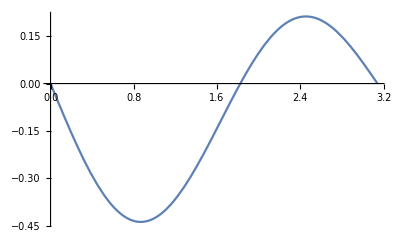

```mathematica
Plot[signalXS[ArcTan[3.4/6.8],β]/.dmJ->π/4,{β,0,π}]
```

```mathematica
signalXud[ArcTan[3.4/6.8]/.dmJ->π/4, β]
```

0.4 Sin[2 dmJ] (0.8 Sin[β]-1.4 Sin[2 β])

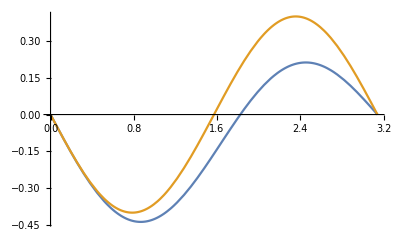

```mathematica
Plot[{signalXS[ArcTan[3.4/6.8],β]/.dmJ->π/4,(signalXud[ArcTan[3.4/6.8], β]+signalXdu[ArcTan[3.4/6.8], β])/2/.dmJ->π/4},{β,0,π}]
```

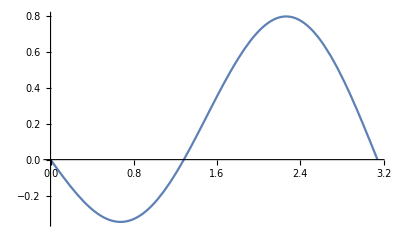

```mathematica
Plot[signalXud[ArcTan[3.4/6.8], β]/.dmJ->π/4,{β,0,π}]
```

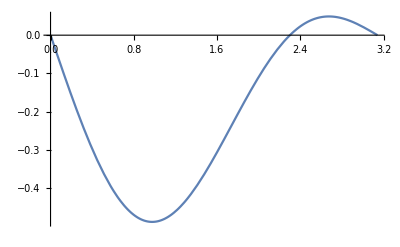

```mathematica
Plot[signalXdu[ArcTan[3.4/6.8], β]/.dmJ->π/4,{β,0,π}]
```

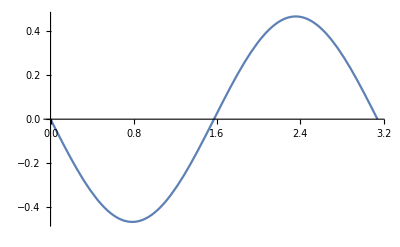

```mathematica
Plot[signalXdu[ArcTan[3.4/6.8], π/4],{dmJ,0,π}]
```

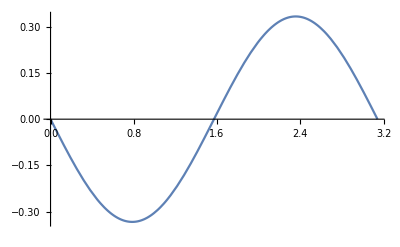

```mathematica
Plot[signalXud[ArcTan[3.4/6.8], π/4],{dmJ,0,π}]
```

```mathematica
Plot[signalXud[ArcTan[3.4/6.8], π/4],{dmJ,0,π}]
```

-Graphics-